## 6.859 A4: Does Charlie WFH?

## Georgios Varnavides, Max L’Etoille

## “Time” Panel

### Employment Data

```mathematica
SetDirectory[FileNameDrop[NotebookDirectory[],-2]]
```

/home/george/Documents/git-repos/a4-does-charlie-wfh

```mathematica
Import["data/Employment-City-Daily.csv",{"Data",1}]
```

{year,month,day,countyfips,emp_combined,emp_combined_inclow,emp_combined_incmiddle,emp_combined_inchigh}

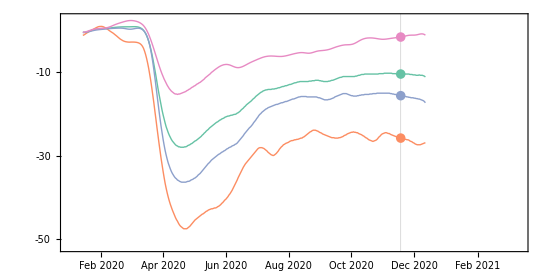

```mathematica
employmentData=Import["data/Employment-City-Daily.csv","HeaderLines"->1];
employmentPlot=With[{
ts=TimeSeries/@Transpose[(Thread[{DateObject[{#1,#2,#3}],100{#5,#6,#7,#8}}]&@@@employmentData)],
cols=ResourceFunction["ColorBrewerData"]["Set2",4]
},DateListPlot[ts,ImageSize->550,FrameTicks->{{Range[-50,10,10],None},{Automatic,None}},PlotStyle->(Directive[Thick,#]&/@cols),DateTicksFormat->{"MonthNameShort", " ", "YearShort"},ImagePadding->All,LabelStyle->Directive[14,Black],GridLines->{{DateObject[{2020,11,18},"Day","Gregorian",-4.]},None},Epilog->{PointSize[0.0125],Thread[{cols,Point[{DateObject[{2020,11,18},"Day","Gregorian",-4.],#[DateObject[{2020,11,18},"Day","Gregorian",-4.]]}]&/@ts}]},PlotRange->{{DateObject[{2020,1,1}],DateObject[{2021,3,13}]},{-52,3}},AspectRatio->1/2]]
```

### COVID Data

```mathematica
covidData=Import["data/COVID-City-Daily.csv","HeaderLines"->1];
```

```mathematica
Import["data/COVID-City-Daily.csv",{"Data",1}]
```

{year,month,day,cityid,new_case_count,new_death_count,new_test_count,new_case_rate,new_death_rate,new_test_rate,case_count,case_rate,death_count,death_rate,test_count,test_rate}

```mathematica
Select[{DateObject[{#1,#2,#3}],#8}&@@@Select[covidData,#[[4]]==25&],#[[1]]==DateObject[{2020,12,25}]&]
```

{{Fri 25 Dec 2020,52.5}}

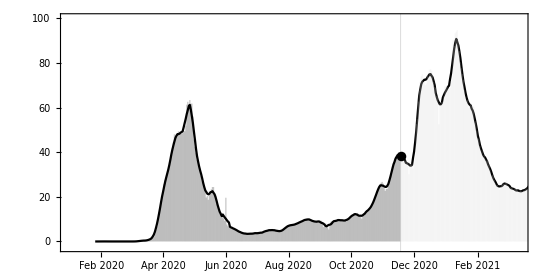

```mathematica
covidPlot=Block[{suffolkCountyData=Select[covidData,#[[4]]==25&],ts,movingAverage},
ts={DateObject[{#1,#2,#3}],#8}&@@@suffolkCountyData;
movingAverage=MovingMap[Mean,ts,{Quantity[7,"Day"],Center}];
MapAt[DeleteCases[#,_Point,Infinity]&,
DateListPlot[Append[TakeDrop[ts,Floor[Length[ts]0.7]],movingAverage],Filling->{1->0,2->0},Joined->{False,False,True},ImageSize->550,PlotStyle->{Black,LightGray,Black},GridLines->{{DateObject[{2020,11,18},"Day","Gregorian",-4.]},None},Epilog->{Black,PointSize[0.0125],Point[{DateObject[{2020,11,18},"Day","Gregorian",-4.],TimeSeries[movingAverage][DateObject[{2020,11,18},"Day","Gregorian",-4.]]}]},PlotRange->{{DateObject[{2020,1,1}],DateObject[{2021,3,13}]},{-2.5,100}},FrameTicks->{{Range[0,100,20],None},{Automatic,None}},LabelStyle->Directive[14,Black],DateTicksFormat->{"MonthNameShort", " ", "YearShort"},AspectRatio->1/2],1]]
```

### Validations Per Line

```mathematica
linesValidationsData =Import["data/mbta-gated-station-validations-by-line-01_2018-03_2021.csv","HeaderLines"->1];
Keys[linesValidationsDataGroupedByLine=KeySort@KeyDrop[GroupBy[MapAt[DateObject,linesValidationsData,{All,1}],#[[2]]&]//Quiet,"Silver Line"]]
linesValidationsDataGroupedByLine=Map[Delete[#,2]&,linesValidationsDataGroupedByLine,{2}];
```

{Blue Line,Green Line,Orange Line,Red Line}

```mathematica
lineValidationsDataNoWeekends=Map[Select[#,First[#]["DayName"]≠Saturday&&First[#]["DayName"]≠Sunday&]&,linesValidationsDataGroupedByLine];
lineValidationsDataWeekMovingAverage=TimeSeriesResample[TimeSeries[MovingMap[Mean,#,{Quantity[2,"Weeks"],Right}]]]&/@lineValidationsDataNoWeekends;
```

```mathematica
seasonallyAdjustedDates=Range[#1+365 24 60 60,#2-13 24 60 60,24 60 60]&@@{AbsoluteTime[lineValidationsDataWeekMovingAverage["Red Line"]["FirstDate"]],AbsoluteTime[lineValidationsDataWeekMovingAverage["Red Line"]["LastDate"]]};
```

```mathematica
seasonallyAdjustedValidationsTimeseriesLines[line_]:=TimeSeries[Thread[{FromAbsoluteTime/@seasonallyAdjustedDates,100.((lineValidationsDataWeekMovingAverage[line][seasonallyAdjustedDates]-lineValidationsDataWeekMovingAverage[line][seasonallyAdjustedDates-365 24 60 60])/lineValidationsDataWeekMovingAverage[line][seasonallyAdjustedDates-365 24 60 60])}]]
```

```mathematica
seasonallyAdjustedRidershipData=Join@@Table[Flatten/@MapAt[Append[Take[First[#],3],First[StringSplit[line]]]&,seasonallyAdjustedValidationsTimeseriesLines[line]["DatePath"],{All,1}],{line,{"Blue Line","Green Line","Orange Line","Red Line"}}]
```

```mathematica
Export["data/mbda-gated-station-validations-by-line-seasonally-adjusted.csv",Prepend[seasonallyAdjustedRidershipData,{"year","month","day","line","ridership"}]]
```

data/mbda-gated-station-validations-by-line-seasonally-adjusted.csv

```mathematica
validationPlot["Blue Line"]=With[{ts=seasonallyAdjustedValidationsTimeseriesLines["Blue Line"]},DateListPlot[ts,PlotStyle->Blue,PlotRange->{{DateObject[{2020,1,1}],DateObject[{2021,3,13}]},{-100,20}},GridLines->{{DateObject[{2020,11,18},"Day","Gregorian",-4.]},Range[-75,25,25]},GridLinesStyle->LightGray,Epilog->{Blue,PointSize[0.0125],Point[{DateObject[{2020,11,18},"Day","Gregorian",-4.],ts[DateObject[{2020,11,18},"Day","Gregorian",-4.]]}]},AspectRatio->1/8,ImageSize->550,FrameTicks->{{Range[-75,25,25],None},{None,None}},LabelStyle->Directive[14,Black],DateTicksFormat->{"MonthNameShort", " ", "YearShort"}]];

validationPlot["Green Line"]=With[{ts=seasonallyAdjustedValidationsTimeseriesLines["Green Line"]},DateListPlot[ts,PlotStyle->RGBColor[0,1/3,0],PlotRange->{{DateObject[{2020,1,1}],DateObject[{2021,3,13}]},{-100,20}},GridLines->{{DateObject[{2020,11,18},"Day","Gregorian",-4.]},Range[-75,25,25]},GridLinesStyle->LightGray,Epilog->{RGBColor[0,1/3,0],PointSize[0.0125],Point[{DateObject[{2020,11,18},"Day","Gregorian",-4.],ts[DateObject[{2020,11,18},"Day","Gregorian",-4.]]}]},AspectRatio->1/8,ImageSize->550,FrameTicks->{{Range[-75,25,25],None},{None,None}},LabelStyle->Directive[14,Black],DateTicksFormat->{"MonthNameShort", " ", "YearShort"}]];

validationPlot["Orange Line"]=With[{ts=seasonallyAdjustedValidationsTimeseriesLines["Orange Line"]},DateListPlot[ts,PlotStyle->Orange,PlotRange->{{DateObject[{2020,1,1}],DateObject[{2021,3,13}]},{-100,20}},GridLines->{{DateObject[{2020,11,18},"Day","Gregorian",-4.]},Range[-75,25,25]},GridLinesStyle->LightGray,Epilog->{Orange,PointSize[0.0125],Point[{DateObject[{2020,11,18},"Day","Gregorian",-4.],ts[DateObject[{2020,11,18},"Day","Gregorian",-4.]]}]},AspectRatio->1/8,ImageSize->550,FrameTicks->{{Range[-75,25,25],None},{None,None}},LabelStyle->Directive[14,Black],DateTicksFormat->{"MonthNameShort", " ", "YearShort"}]];

validationPlot["Red Line"]=With[{ts=seasonallyAdjustedValidationsTimeseriesLines["Red Line"]},DateListPlot[ts,PlotStyle->Red,PlotRange->{{DateObject[{2020,1,1}],DateObject[{2021,3,13}]},{-100,20}},GridLines->{{DateObject[{2020,11,18},"Day","Gregorian",-4.]},Range[-75,25,25]},GridLinesStyle->LightGray,Epilog->{Red,PointSize[0.0125],Point[{DateObject[{2020,11,18},"Day","Gregorian",-4.],ts[DateObject[{2020,11,18},"Day","Gregorian",-4.]]}]},AspectRatio->1/8,ImageSize->550,FrameTicks->{{Range[-75,25,25],None},{None,None}},LabelStyle->Directive[14,Black],DateTicksFormat->{"MonthNameShort", " ", "YearShort"}]];
```

### Time Line

```mathematica
timeline={
<|"Schools Closed Down"->DateObject[{2020,3,17},"Day","Gregorian",-4.],"National Emergency Declared"->DateObject[{2020,3,13},"Day","Gregorian",-4.]|>,
<|"Stay at Home Order"->DateInterval[…],"Second Stay at Home Order"->DateObject[{2020,11,6},"Day","Gregorian",-4.]|>,
<|"Nonessential Businesses Shutdown"->DateInterval[…],"Second Nonessential Businesses Shutdown"->DateObject[{2020,12,13},"Day","Gregorian",-4.]|>,
<|"First Stimulus Checks Start"->DateObject[{2020,4,15},"Day","Gregorian",-4.],"Second Stimulus Checks Start"->DateObject[{2021,1,4},"Day","Gregorian",-4.]|>};
```

```mathematica
timelinePlot=TimelinePlot[timeline,PlotRange->{{DateObject[{2020,1,1}],DateObject[{2021,3,13}]},Automatic},AspectRatio->1/2,ImageSize->550,LabelStyle->Directive[14,Black],DateTicksFormat->{"MonthNameShort", " ", "YearShort"},PerformanceGoal->"Speed",PlotTheme->"Monochrome",PlotLayout->"Grouped"]
```

-Graphics-

### Combined

```mathematica
timePanel=GraphicsColumn[{
Show[timelinePlot,ImagePadding->{{40,20},{Automatic,Automatic}}],
Show[covidPlot,ImagePadding->{{40,20},{Automatic,Automatic}}],
Show[employmentPlot,ImagePadding->{{40,20},{Automatic,Automatic}}],
Show[validationPlot["Blue Line"],ImagePadding->{{40,20},{Automatic,Automatic}}],
Show[validationPlot["Green Line"],ImagePadding->{{40,20},{Automatic,Automatic}}],
Show[validationPlot["Orange Line"],ImagePadding->{{40,20},{Automatic,Automatic}}],
Show[validationPlot["Red Line"],ImagePadding->{{40,20},{Automatic,Automatic}}]},ImageSize->550]
```

-Graphics-

### Margins shennanigans

```mathematica
Take[(FullSimplify[height-Partition[Accumulate[Append[
Prepend[
Riffle[ConstantArray[(height-marginTop-marginBottom-padding 2)/3,3],padding],marginBottom],
marginTop]],2,1]]//Reverse),{2,-1,2}]/.{marginTop->margin.top,marginBottom->margin.bottom,padding->"padding_between_charts"}
```

{{1/3 (-2 padding_between_charts+height-margin.bottom+2 margin.top),margin.top},{1/3 (-padding_between_charts+2 height-2 margin.bottom+margin.top),1/3 (padding_between_charts+height-margin.bottom+2 margin.top)},{height-margin.bottom,1/3 (2 padding_between_charts+2 height-2 margin.bottom+margin.top)}}

```mathematica
Simplify[height-Partition[Accumulate[Prepend[ConstantArray[(1/3 (height-marginBottom-marginTop-2 padding))/4,4],marginBottom]]//Simplify,2,1]]//Reverse
```

{{1/4 (3 height-3 marginBottom+marginTop+2 padding),1/3 (2 height-2 marginBottom+marginTop+2 padding)},{1/6 (5 height-5 marginBottom+marginTop+2 padding),1/4 (3 height-3 marginBottom+marginTop+2 padding)},{1/12 (11 height-11 marginBottom+marginTop+2 padding),1/6 (5 height-5 marginBottom+marginTop+2 padding)},{height-marginBottom,1/12 (11 height-11 marginBottom+marginTop+2 padding)}}